## Willem Nielsen Work

### DONE: Perturbation function, vis function TODO: make memoize function, catalogue lifetime results in disease space, for different stages, locations, intensities, genotypes and phenotypes. Vis results, draw conclusions.

### Functions

#### Old Viz

```mathematica
plotca[ca_, OptionsPattern[{ColorRules->customstyledata["Colors"], ArrayPlot}]]:= ArrayPlot[ca, ColorRules -> customstyledata["Colors"],
   Mesh -> True, MeshStyle -> Opacity[.1], ImageSize -> OptionValue[ImageSize]
   ]
   
plotrule[rule_, OptionsPattern[{ColorRules->customstyledata["Colors"], ArrayPlot}]]:= Module[{digits},
digits = IntegerDigits[rule[[1]], rule[[2]], 27];
plotca[{digits}, ImageSize->OptionValue[ImageSize]]
]

Options[plot] = {"init"->initconditions, "padding"->1, "nsteps"->Automatic};
plot[{ruleidx_, k_, r_}, OptionsPattern[{ColorRules->customstyledata["Colors"], ArrayPlot, plot}]] :=  
Module[
{steps = If[SameQ[OptionValue["nsteps"], Automatic], Max[testlifetime[{ruleidx, k, r}, 200], 15], OptionValue["nsteps"]],ca},
  ca = ArrayPad[#, OptionValue["padding"]]& /@ getca[{ruleidx, k, r}, OptionValue["init"], steps];
  ArrayPlot[ca,  ColorRules->OptionValue[ColorRules],
   Mesh -> True, MeshStyle -> Opacity[.1], ImageSize -> OptionValue[ImageSize]
   ]]
```

```mathematica
customstyledata = {{"[◼]", "CustomStyleData"}}; analyzeevolution = {{"[◼]", "AnalyzeEvolution"}};
```

#### Perturbation Viz

```mathematica
TrimCA[pat_,{width_,height_}]:=Module[
  {
    w,h,ranges,left,right,lt
  },
  w=If[
    width=!=None,
    ranges=DeleteCases[nonzeroRange /@ pat,{}];
    {left,right}={Min[ranges[[All,1]]],Max[ranges[[All,2]]]};
    #[[left-width ;; right+width]] & /@ pat,
    pat
  ];
  
  h=If[
    height=!=None,
    lt=Length[w]-LengthWhile[Reverse[w],Total[#]==0 &];
    w[[ ;; Min[lt+height,Length[w]]]],
    w
  ]
]
```

```mathematica
ClearAll@ShowCADiffs
```

```mathematica
Options[ShowCADiffs] = {"Trim" -> {1, 10}};
ShowCADiffs[pat1_, pat2_, OptionsPattern[{ ArrayPlot, ShowCADiffs}]] := Module[{locs, vals, rus, highlighted, trimmed, colrules},
  locs = getdifflocs[pat1, pat2];
  vals = pat2[[#1, #2]] & @@@ locs;
  rus = MapThread[#1 -> If[#2 == 0, -100, -#2] &, {locs, vals}];
  highlighted = ReplacePart[pat1, rus];
  trimmed = TrimCA[highlighted, OptionValue["Trim"]];
  colrules = 
Join[{0->White, -100 -> GrayLevel[.9]}, 
#1 :> Lighter[#2,.8]&@@@ customstyledata["Colors"],
-#1 :> Darker[#2,.3]& @@@ customstyledata["Colors"]];
  ArrayPlot[trimmed, ColorRules -> colrules, MeshStyle -> Opacity[0.1], ImageSize -> OptionValue[ImageSize]]
  ]
```

```mathematica
ShowPerturbations[initpat_, patlist_, levelspec_] := Map[ShowCADiffs[initpat, #] &, patlist[[1]], levelspec]
```

```mathematica
ShowPerturbationEvolution[initpat_, evo_] := 
 MapThread[ShowPerturbations[initpat, #1, {#2}] &, {evo, Range[Length[evo]]}]
```

#### Perturbation Function

```mathematica
nonzeroRange[list_] := 
Flatten[{FirstPosition[list, Except[0], Heads -> False], 1 + Length[list] - FirstPosition[Reverse[list], Except[0], Heads -> False]}]
```

```mathematica
getdifflocs[pat1_, pat2_] := Position[MapThread[{#1, #2} &, {pat1, pat2}, 2], {x_, y_} /; x != y, 2]
```

```mathematica
towhite[k_, bit_] := {0}
tored[k_, bit_] := {1}
toblue[k_, bit_] := {2}
add1[k_, bit_] := If[bit == k - 1, {0}, {bit + 1}]
sub1[k_, bit_] := If[bit == 0, {k - 1}, {bit - 1}]
flipall[k_, bit_] := Complement[Range[0, k - 1], {bit}]
```

```mathematica
towhite[k_, bit_] := p[0]
tored[k_, bit_] := p[1]
toblue[k_, bit_] := p[2]
add1[k_, bit_] := If[bit == k - 1, p[0], p[bit + 1]]
sub1[k_, bit_] := If[bit == 0, p[k - 1], p[bit - 1]]
```

```mathematica
sortfrom[list_, start_] :=
 Which[
  start == "Left", list,
  start == "Right", ReverseSort[list],
  start == "Center", SortBy[list, Abs[Median[list] - #] &],
  start == "Random", RandomSample[list, Length[list]],
  True, list
  ]
```

```mathematica
ClearAll@PerturbBitRow
```

```mathematica
Options[PerturbBitRow] = {"PerturbRowStart" -> "Left", "PerturbBitFunction" -> add1, "SelectBits" -> All};
PerturbBitRow[row_,rowidx_->rangespec_,k_,OptionsPattern[PerturbBitRow]]:=Module[{},
colidxs = Range@@nonzeroRange[row];
withall = ReplaceAll[rowidx->rangespec, All:> Range[Length[colidxs]]];
ranged = Replace[withall, 
Rule[i_, List[order_String, idxs_]]:> sortfrom[colidxs, order][[Select[idxs, #<=Length[colidxs]&]]]];
filtered = If[OptionValue["SelectBits"]===All, ranged, 
Select[ranged,MemberQ[OptionValue["SelectBits"], row[[#]]]&]];
rus = # -> OptionValue["PerturbBitFunction"][k, row[[#]]]&/@ filtered;
newrow = ReplacePart[row, rus]
]
```

```mathematica
PerturbBitRow[row_,{rowidx_, rangespec_},k_,OptionsPattern[PerturbBitRow]]:=Module[{},
withall = ReplaceAll[rangespec, All:> Range[Length[row]]];
ranged = Select[withall, #<=Length[row]&];
filtered = If[OptionValue["SelectBits"]===All, ranged, 
Select[ranged,MemberQ[OptionValue["SelectBits"], row[[#]]]&]];
rus = # -> OptionValue["PerturbBitFunction"][k, row[[#]]]&/@ filtered;
newrow = ReplacePart[row, rus]
]
```

```mathematica
ClearAll@PerturbCA
```

```mathematica
PerturbCA[{ca_, rule_}, idxspec_, ops:OptionsPattern[PerturbBitRow]] := Module[{},
    perturbedrow = PerturbBitRow[ca[[idxspec[[1]]]],idxspec, rule[[2]], ops];
{ReplacePart[ca, idxspec[[1]]->perturbedrow], rule}

  ]
```

```mathematica
ClearAll@EvolvePerturbedCA
```

```mathematica
EvolvePerturbedCA[{pca_, rule_}]:= Module[{},
pidx = FirstPosition[pca,p[_], {}];
If[pidx == {}, {pca, rule},
prowidx = pidx[[1]];
pre = pca[[;; prowidx- 1]];
prow =pca[[prowidx]]/.p[bit_]:>bit;
perturbedCA = Join[pre, CellularAutomaton[rule, prow, Length[pca] - Length[pre] - 1]];
    {perturbedCA, rule}
]]
```

```mathematica
row: {row->{"Random", {1}}}
row->jmax: {row->{"Random", Range[jmax]}}
row -> {j1, j2...}:  {row->{"Random", {j1, j2...}}}
row ->"Left": {row -> {"Left", 1}}
row ->{"Left", jmax}: {row->{"Left", Range[jmax]}}
{row->{"Order", {j1, j2...}}}
{10->1,15} : {10->1, 15->1}
{{10, 5}}: {{10, 5}}
{{10, {7, 8, 9, 10}}}
{10-> All}
{10, {{90, 100}}}
```

```mathematica
fullform[pertspec_]:= pertspec //. 
{Rule[i_, j_Integer]:> i->Range[j],
Rule[i_, List[j__Integer]]:> i->{"Random", {j}},
Rule[i_, s_String]:> i->{s, {1}},
Rule[i_, {s_String, j_Integer}]:> i->{s, Range[j]},
Rule[i_, List[s_String]]:> i->{s, {1}},
List[List[jmin_Integer, jmax_Integer]]:> Range[jmin, jmax]
 }
```

```mathematica
pairfullform[pertspec_]:= Replace[pertspec,
    {List[i_, j_Integer]:> {i,{j}},
List[i_, List[List[jmin_Integer, jmax_Integer]]]:> {i,Range[jmin, jmax]}}
  ]
```

```mathematica
ClearAll@PerturbedCAEvolution
```

```mathematica
PerturbedCAEvolution[rule_, init_, steps_, pertspec_:"Random"] := 
Module[{ca = CellularAutomaton[rule, init, {steps, All}]},
speclist = 
Replace[pertspec, 
{"Random"->{RandomInteger[{1, steps}]->1},
List[i_Integer, j_Integer]->{{i, j}}, 
List[i_Integer, List[j__]]->{{i,{ j}}},
Rule[i_, j_]->{i->j}, i_Integer:>{i->1}}];
ffs = Replace[speclist, {Rule[i_, j_]:> fullform[i->j], List[i_, j_]:> pairfullform[{i, j}]}, 1];
FoldList[EvolvePerturbedCA[Sow[PerturbCA[#1, #2]]]&, {ca, rule}, ffs]
   ]
```

{{50,{{90,100}}}}

{{50,{90,91,92,93,94,95,96,97,98,99,100}}}

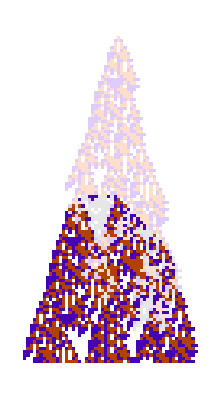

```mathematica
evo = PerturbedCAEvolution[ru, {{1}, 0}, 100, {50, {{90, 100}}}];
speclist
ffs
ShowCADiffs@@evo[[All, 1]]
```

```mathematica
speclist = 
Replace[{10->1, {10, {1, 2, 3}}}, 
{"Random"->{RandomInteger[{1, 101}]->1},
List[i_Integer, j_Integer]->{{i, j}}, 
Rule[i_, j_]->{i->j}, i_Integer:>{i->1}}]
```

{10→1,{10,{1,2,3}}}

```mathematica
ffs = Replace[speclist, {Rule[i_, j_]:> fullform[i->j], List[i_, j_]:> pairfullform[{i, j}]}, 1]
```

{10→{Random,{1}},{10,{1,2,3}}}

```mathematica
pairfullform[{10,{1,2,3}}]
```

{10,{1,2,3}}

```mathematica
speclist = Replace[10, {List[i_Integer, j_Integer]->{{i, j}}, Rule[i_, j_]->{i->j}, i_Integer:>{i->1}}]
```

{10→1}

```mathematica
ffs = tofullform[speclist]
```

10→{Random,{1}}

```mathematica
PerturbedCAEvolution[rule_, init_, steps_, pertspec_:"Random"] := 
Module[{ca = CellularAutomaton[rule, init, {steps, All}]},
tolist =Replace[pertspec,{s_String?(# === "Random"&):>RandomInteger[{1, Length[ca]}],i_Integer:>{i->1},Rule[i_,j_]:>{i->j},{i_Integer, j_Integer}:>{{i, j}}}];
allruorpair = Replace[pertspec, i_Integer:>i->1, 1];
FoldList[PerturbCA, {ca, rule}, allruorpair]
   ]
```

```mathematica
PerturbedCACombs[{pat_, rule_}, nrow_ -> nperts_, OptionsPattern[PerturbCA]] := Module[{},
  row = pat[[nrow]];
  colidxs = Range @@ nonzeroRange[row];
  sorted = sortidxs[colidxs, OptionValue["PerturbationStart"]];
  prow = ReplacePart[row, # -> OptionValue["PerturbationFunction"][rule[[2]], row[[#]]] & /@ sorted[[;; Min[nperts, Length[colidxs]]]]];
  allrows = Tuples[Replace[prow, x_Integer :> {x}, {1}]];
  pre = pat[[;; nrow - 1]];
  postpats = CellularAutomaton[rule, #, Length[pat] - Length[pre] - 1] & /@ allrows;
   {Join[pre, #], rule} & /@ postpats
  ]
```

```mathematica
Options[PerturbeRows] = {"PerturbationStart" -> "Left", "PerturbationFunction" -> add1, "Width" -> All};
PerturbeRows[{pats_, rule_, levelspec_}, nrow_ -> nperts_, op : OptionsPattern[PerturbeRow]] := Module[{},
  {{Map[PerturbeRow[#, rule, nrow -> nperts, op] &, pats, levelspec], rule, levelspec + 1}}
  ]
```

```mathematica
PerturbedCAEvolution[rule_, init_, steps_, perts_ ] := Module[{pat = CellularAutomaton[rule, init, {steps, All}]},
Echo[plotca[pat]];
  FoldList[PerturbeRows, {{pat}, rule, {1}}, Replace[perts, x_Integer :> x -> 1, {1}]]
  ]
```

```mathematica
tofullform[pertspec_]:= Replace[pertspec,
{
i_Integer:> i->{"Random", {1}},
Rule[i_Integer, jmax_Integer]:> i->{"Random", Range[jmax]},
Rule[i_Integer, List[js__Integer]]:> i->{"Random", {js}},
Rule[i_Integer, s_String]:> i->{s, {1}},
Rule[i_Integer, List[s_String, jmax_Integer]]:> i->{s,Range[jmax]},
Rule[i_Integer, List[s_String, List[jmin_Integer, jmax_Integer]]]:>i->{s,Range[jmin, jmax]},
Rule[i_Integer, List[List[jmin_Integer, jmax_Integer]]]:>i->{s,Range[jmin, jmax]}}, 
1
]
```

### Init

```mathematica
ru = {6006804516645,3,1};
initpat =CellularAutomaton[ru,{{1}, 0},{100,All}];
```

### All diseases

```mathematica
alldis = Table[PerturbeRow[{initpat, ru},i->j, "PerturbationStart"->"Right"], {i,1, 92}, {j,1, 10}];
```

```mathematica
center =  Table[PerturbeRow[{initpat, ru},i->j, "PerturbationStart"->"Center"], {i,1, 92}, {j,1, 10}];
```

```mathematica
left =  Table[PerturbeRow[{initpat, ru},i->j, "PerturbationStart"->"Left"], {i,1, 92}, {j,1, 10}];
```

```mathematica
white =  Table[PerturbeRow[{initpat, ru},i->j, "PerturbationStart"->"Left", "PerturbationFunction"->towhite], {i,1, 92}, {j,1, 10}];
```

```mathematica
red =  Table[PerturbeRow[{initpat, ru},i->j, "PerturbationStart"->"Left", "PerturbationFunction"->tored], {i,1, 92}, {j,1, 10}];
```

```mathematica
blue=  Table[PerturbeRow[{initpat, ru},i->j, "PerturbationStart"->"Left", "PerturbationFunction"->toblue], {i,1, 92}, {j,1, 10}];
```

```mathematica
all=  Table[PerturbeRow[{initpat, ru},i->j, "PerturbationStart"->"Center", "PerturbationFunction"->flipall], {i,1, 92}, {j,1, 4}];
```

$Aborted

### Increasing Disease Age

#### add1 Right 1

```mathematica
colrules
```

Join[0→GrayLevel[1],-100→GrayLevel[0.9],{0:>Lighter[GrayLevel[1],0.8],1:>Lighter[Hue[0.06, 1, 1],0.8],2:>Lighter[Hue[0.73, 1, 1],0.8],3:>Lighter[Hue[0.14, 0.81, 0.99],0.8]},{0:>Darker[GrayLevel[1],0.8],-1:>Darker[Hue[0.06, 1, 1],0.8],-2:>Darker[Hue[0.73, 1, 1],0.8],-3:>Darker[Hue[0.14, 0.81, 0.99],0.8]}]

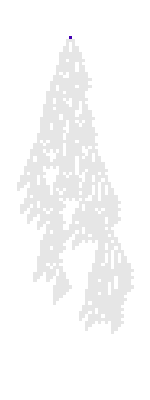
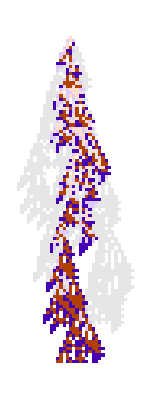
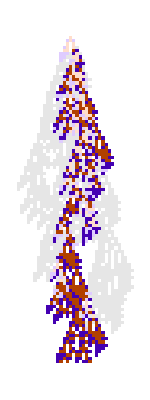
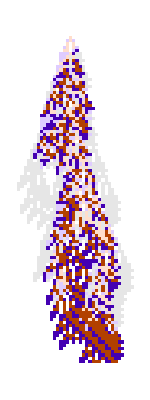
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ShowCADiffs[initpat, #, "Trim"->{1, None}]&/@  alldis[[;;5, 1, 1, 1]]
```

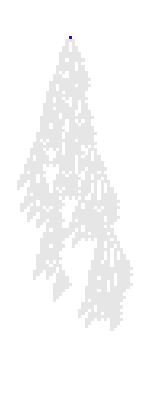
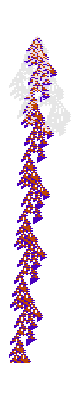
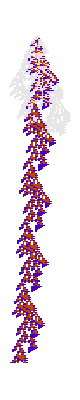
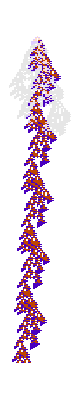
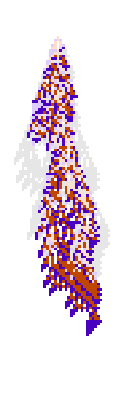
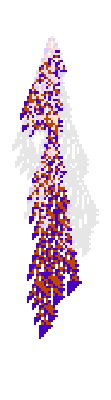
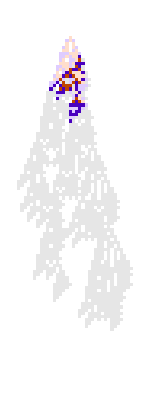
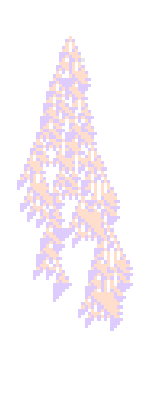
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ShowCADiffs[initpat, #]&/@  alldis[[All, 1, 1, 1]]
```

#### add1 Right 5

```mathematica
ShowCADiffs[initpat, #]&/@  alldis[[All, 5, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### add1 Right 10

```mathematica
ShowCADiffs[initpat, #]&/@  alldis[[All, 10, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### add1 Center 1

```mathematica
ShowCADiffs[initpat, #]&/@  center[[All, 1, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### add1 Center 5

```mathematica
ShowCADiffs[initpat, #]&/@  center[[All, 5, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### add1 Center 10

```mathematica
ShowCADiffs[initpat, #]&/@  center[[All, 10, 1, 1]]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Symbol[]

#### add1 Left 1

```mathematica
ShowCADiffs[initpat, #]&/@  left[[All, 1, 1, 1]]
```

Integer[]

#### add1 Left 5

```mathematica
ShowCADiffs[initpat, #]&/@  left[[All, 5, 1, 1]]
```

Integer[]

#### add1 Left 10

```mathematica
ShowCADiffs[initpat, #]&/@  left[[All, 10, 1, 1]]
```

Integer[]

#### towhite Center 1

```mathematica
ShowCADiffs[initpat, #]&/@  white[[All, 1, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### towhite Center 5

```mathematica
ShowCADiffs[initpat, #]&/@  white[[All, 5, 1, 1]]
```

#### tored Center 1

```mathematica
ShowCADiffs[initpat, #]&/@  red[[All, 1, 1, 1]]
```

#### tored Center 5

```mathematica
ShowCADiffs[initpat, #]&/@  red[[All, 5, 1, 1]]
```

### Increasing Disease Intensity

```mathematica
Length/@alldis[[1, All, 1, 1]]
```

{301,301,301,301,301,301,301,301,301,301}

```mathematica
ShowCADiffs[initpat, #]&/@  alldis[[10, All, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ShowCADiffs[initpat, #]&/@  alldis[[40, All, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ShowCADiffs[initpat, #]&/@  alldis[[70, All, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Single Round

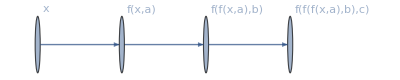

```mathematica
ResourceFunction["FoldGraph"][f,{x},{a,b,c},VertexLabels->Automatic]
```

```mathematica
PerturbeRow[{initpat}]
```

PerturbeRow[test]

```mathematica
ru = {6006804516645,3,1};
initpat =CellularAutomaton[ru,{{1}, 0},{100,All}];
(*p = PerturbeRows[{{initpat, initpat}, ru, {1}}, 10->1];
p2 = PerturbeRows[{p[[1]], ru, {2}}, 10->1];*)
```

```mathematica
p = PerturbedCAEvolution[ru, {{1}, 0}, 100, {10->1, 15->1}];
```

$Aborted

```mathematica
pp1 = PerturbePoint[{initpat, ru}, {10, 1}, "PerturbationFunction"->]
```

add1

```mathematica
pp2 = PerturbePoint[pp1[[1]],{15,1}]
```

add1

flipall

flipall

flipall

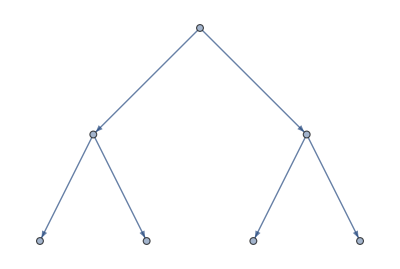

```mathematica
pp = ResourceFunction["FoldGraph"][PerturbePoint[#1,#2, "PerturbationFunction"->flipall]&, {{initpat, ru}}, {{10, 1}, {15, 1}}]
```

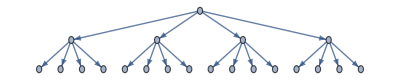

```mathematica
pp = ResourceFunction["FoldGraph"][PerturbeRow[#1,#2, "PerturbationFunction"->flipall]&, {{initpat, ru}}, {10->2, 15-> 2}]
```

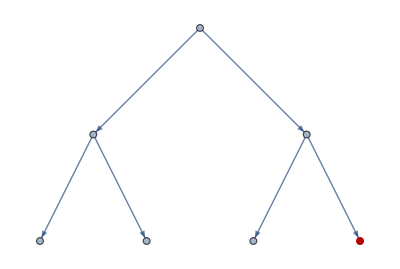

```mathematica
HighlightGraph[pp, VertexList[pp][[7]]]
```

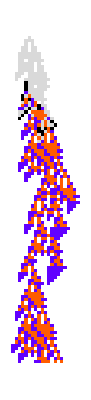
{-Graphics-,-Graphics-}

```mathematica
ShowCADiffs@@@Partition[VertexList[pp][[All, 1]], 2, 1]
```

```mathematica
Length[pp[[1]]]
```

2

```mathematica
ShowCADiffs[pp1[[1, 1]], pp2[[1, 1]]]
```

-Graphics-

```mathematica
Rest@ShowPerturbationEvolution[initpat, p]
```

{{{-Graphics-}},{{{-Graphics-}}}}

```mathematica
Replace[{10->1},x_Integer:>x->1,{1}]
```

{10→1}

```mathematica
Length[p[[2, 1, 1, 1]]]
```

101

```mathematica
Map[Length[#[[1]]]&, p]
```

{1,1}

```mathematica
Map[Length[#] &, p[[1, 1]], {1}]
```

{101}

```mathematica
getfirst[list_, level_]:= list[[#]]&@@Table[1, level]
```

```mathematica
getfirst[{{{1}}}, 1]
```

{{1}}

```mathematica
p[[#]]&@@Table[1, {1}[[1]]][[1]]
```

1

```mathematica
Map[ShowCADiffs[initpat,#] &, p[[2, 1]], {2}]
```

{{-Graphics-}}

```mathematica
ShowPerturbations[initpat, p[[2]], {2}]
```

{{-Graphics-}}

```mathematica
Map[ShowCADiffs[initpat, #]&, p2[[1]], {3}]
```

{{{-Graphics-}},{{-Graphics-}}}

```mathematica
Length[o[[1,2, 1]]]
```

101

```mathematica
Length[o[[1, 1]]]
```

1

```mathematica
p =PerturbeRow[pat,ru,10->1, "PerturbationStart"->"Center","PerturbationFunction"->flipall];
```

```mathematica
Options[ShowCADiffs]
```

{Trim→{1,10}}

2

```mathematica
plotca[pat]
```

-Graphics-

```mathematica
plotca@TrimCA[pat, {1, 10}]
```

-Graphics-

```mathematica
ShowCADiffs[pat, #]&@ p[[1]]
```

{}

{1,10}

-Graphics-

```mathematica
ArrayPlot[TrimCA[highlighted, {1, 10}], ColorRules->Join[#[[1]]*-1->#[[2]]&/@ customstyledata["Colors"], { -100->Black,_Integer->LightGray}]]
```

-Graphics-

#### All possible

```mathematica
ps = Table[PerturbePattern[{pat, ru},i->j, "PerturbationStart"->"Right", "Cut"->300, "PerturbationFunction"->towhite], {i,5, 10}, {j,1, 10}];
```

```mathematica
ps = Table[PerturbePattern[{pat, ru}, {10, i}, "PerturbationStart"->"Right", "Cut"->300, "PerturbationFunction"->add1], {i,1, 10}];
```

```mathematica
Map[showpatdiffs[pat, #, "Trim"->True]&,  ps[[ All, 1, 1]],{2}]
```

{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}

```mathematica
t1_Integer : t1->1
```

```mathematica
10: 10->{1}
10->5: 10->{1, 2, 3, 4, 5}
10->{{5, 7}}: 10->{5, 6, 7}
10->{5, 6}: 10->{5, 6}
```

```mathematica
ReplaceAll[<|1->{{5,"Enumeration"}}|>, Rule[1,_]:>"h"]
```

<|1→{{5,Enumeration}}|>

```mathematica
assoc=<|"a"->1,"b"->2,"c"->3|>;
newAssoc=Replace[assoc,"b"->_:>("b"->42),{1}]
(*Output:<|"a"->1,"b"->42,"c"->3|>*)
```

<|a→1,b→2,c→3|>

## SW Notes

#### How to store results of perturbations

```mathematica
{1,2,0,1,p[0,1],XXXX}
```

```mathematica
p[_,1]->XXX
```

```mathematica
PerturbedCAEvolution[   ]
```

```mathematica
PerturbationIndicatorFunction->
```

```mathematica
p[0,1]
```

```mathematica
{0,1}
```

```mathematica
Apply[p]
```

```mathematica
Last
```

```mathematica
-#[[2]]&
```

```mathematica
<|0->XXX,1->2,2->0|>
```

#### How to specify perturbations

```mathematica
<|1->{{5,"Enumeration"}}|>
```

```mathematica
<|1->{{5,"Random"},{6,"Random"}}|>
```

```mathematica
<|1->{{5,f},{6,"Random"}}|>
```

```mathematica
5
```

```mathematica
{5,First}
```

```mathematica
Range[6]
```

{1,2,3,4,5,6}

```mathematica
Range[4,11]
```

{4,5,6,7,8,9,10,11}

```mathematica
First[ ]
```

```mathematica
Last[   ]
```

### Analysis functions

lifetime after perturbation   [ AKA fitness ]

number of cells that stay the same after perturbation

### ML for therapy

Fitness function is either (a) how many cells we can return to their original state, or (b) how close we can get the lifetime to the original